## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

## 设置non-GR参数字符flag Gw@150914!

```mathematica
eventID="GW150914_095045";

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l"];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l"];

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l",7];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l","cpsi7"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l","psi7"];
```

```mathematica
csvPath="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventID;
csvNames=eventID<>"_"<>#<>".csv"& /@ deviationNames;

csvFilePaths=csvPath<>"\\"<>#& /@ csvNames;
```

### from CSV

```mathematica
samples=<||>;
Do[
CSVSamples=Import["D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv\\"<>eventID<>"\\"<>eventID<>"_"<>n<>".csv"];
samples[n]=<||>;
samples[n]["mass1"]=CSVSamples[[All,1]][[2;;]];
samples[n]["mass2"]=CSVSamples[[All,2]][[2;;]];
samples[n]["spin1z"]=CSVSamples[[All,3]][[2;;]];
samples[n]["spin2z"]=CSVSamples[[All,4]][[2;;]];
samples[n]["eta"]=CSVSamples[[All,5]][[2;;]];
samples[n]["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[n][n]=CSVSamples[[All,7]][[2;;]];
samples[n]["chis"]=χs[samples["spin1z"],samples["spin2z"]];
samples[n]["chia"]=χa[samples["spin1z"],samples["spin2z"]];,
{n,deviationNames}
]
```

### Calculate GR Coefficients

```mathematica
Do[
samples[deviationNames[[n]]][psiNames[[n]]]=MapThread[
Psi[deviationOrders[[n]],η[#1,#2],M[#1,#2],#3,#4]&,
{samples[deviationNames[[n]]]["mass1"],samples[deviationNames[[n]]]["mass2"],samples[deviationNames[[n]]]["spin1z"],samples[deviationNames[[n]]]["spin2z"]}
];,
{n,Range[Length[deviationOrders]]}
]
```

### Calculate BCIs

```mathematica
BCI=<||>;
Do[
BCI[deviationNames[[n]]]=<||>;
BCI[deviationNames[[n]]]["mass1"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass1"],Subscript["m","1"]][[1]];
BCI[deviationNames[[n]]]["mass2"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass2"],Subscript["m","2"]][[1]];
BCI[deviationNames[[n]]]["spin1z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin1z"],"spin1z"][[1]];
BCI[deviationNames[[n]]]["spin2z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin2z"],"spin2z"][[1]];
BCI[deviationNames[[n]]][deviationNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][deviationNames[[n]]],deviationNames[[n]]][[1]];
BCI[deviationNames[[n]]][psiNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][psiNames[[n]]],psiNames[[n]]][[1]];,
{n,Range[Length[deviationOrders]]}
]
```

```mathematica
widths={};
Do[
AppendTo[widths,(BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]])/(BCI[deviationNames[[n]]][psiNames[[n]]][[3]]-BCI[deviationNames[[n]]][psiNames[[n]]][[1]])],
{n,Range[Length[deviationOrders]]}
];
Round[widths,0.0001]
widths={};
Do[
AppendTo[widths,BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]]],
{n,Range[Length[deviationOrders]]}
];
Round[widths/{5000,250,150,5,1.5,0.5,0.1},0.0001]
```

{0.2795,2.3274,0.6996,23.1717,1.3101,3.0098,21.6687,3.7931}

Thread::tdlen: Objects of unequal length in {729.758,260.535,100.618,67.4343,8.80747,12.5765,2.55698,4.12718} {1/5000,1/250,1/150,1/5,0.666667,2.,10.} cannot be combined.

Round[{1/5000,1/250,1/150,1/5,0.666667,2.,10.} {729.758,260.535,100.618,67.4343,8.80747,12.5765,2.55698,4.12718},0.0001]

```mathematica
o="5l";
{Quantile[samples["cpsi"<>o]["psi"<>o],{0.05,0.95}]-Median[samples["cpsi"<>o]["psi"<>o]],Median[samples["cpsi"<>o]["psi"<>o]]}
```

{{-2.96206,3.76067},16.9839}

```mathematica
medians={};
Do[
AppendTo[medians,BCI[deviationNames[[n]]][deviationNames[[n]]][[2]]/BCI[deviationNames[[n]]][psiNames[[n]]][[2]]],
{n,Range[Length[deviationOrders]]}
];
Round[medians,0.0001]
```

{0.5485,1.4989,-0.8617,7.2556,-2.3611,8.2852,9.4325,3.5929}

## m1-m2 Plot, 22

```mathematica
pInterval=<||>;
tapeIntervals=<||>;
tapes=<||>;
plots=<||>;
compPlots=<||>;
lines=<||>;
legends=<||>;

m1m2=<||>;
m1PriorRange=<||>;
m2PriorRange=<||>;
m1m2PDF=<||>;
contourPD=<||>;
contourPlotObj=<||>;
contourPoints=<||>;
smoothedContourPoints=<||>;
```

```mathematica
BCI
```

<|cpsi0→<|mass1→{34.2952,38.7241,43.5807},mass2→{21.578,26.1268,30.6144},spin1z→{-0.124713,0.21145,0.51277},spin2z→{-0.904911,-0.416623,0.128903},cpsi0→{4975.9,5328.8,5705.72},psi0→{8585.35,9718.19,11193.5}|>,cpsi2→<|mass1→{34.7374,38.7448,43.2507},mass2→{21.7936,26.5548,31.1279},spin1z→{-0.119725,0.224662,0.511227},spin2z→{-0.858863,-0.392509,0.0545219},cpsi2→{786.987,900.256,1047.28},psi2→{567.031,615.352,677.519}|>,cpsi4→<|mass1→{36.8673,41.417,46.1343},mass2→{20.2368,24.147,28.5042},spin1z→{-0.0832028,0.122299,0.336979},spin2z→{-0.83623,-0.382553,-0.0118634},cpsi4→{282.143,312.529,348.36},psi4→{43.0916,44.584,46.9235}|>,cpsi5l→<|mass1→{34.3293,38.535,42.919},mass2→{22.2419,26.947,31.1513},spin1z→{0.0344537,0.376998,0.660192},spin2z→{-0.970087,-0.780869,-0.281019},cpsi5l→{-45.0515,-40.5121,-36.4492},psi5l→{13.7338,16.4868,19.5773}|>,cpsi6→<|mass1→{36.9691,41.0014,44.9468},mass2→{21.9583,25.4562,30.2585},spin1z→{0.0620261,0.32919,0.54777},spin2z→{-0.96963,-0.737916,-0.247651},cpsi6→{-58.8724,-52.7236,-45.9694},psi6→{-7.1402,-5.29733,-3.30982}|>,cpsi6l→<|mass1→{33.4206,38.2222,43.6814},mass2→{22.1108,27.019,31.2844},spin1z→{-0.0949733,0.219502,0.503361},spin2z→{-0.950426,-0.625143,-0.192696},cpsi6l→{-11.1773,-9.87389,-8.62533},psi6l→{-1.13566,-1.05507,-1.01396}|>,cpsi7→<|mass1→{31.3765,36.0345,42.3329},mass2→{21.7756,27.0328,30.877},spin1z→{-0.132683,0.26195,0.626339},spin2z→{-0.914543,-0.451452,0.179172},cpsi7→{1.74449,3.89748,6.04668},psi7→{0.536586,1.07986,1.56722}|>|>

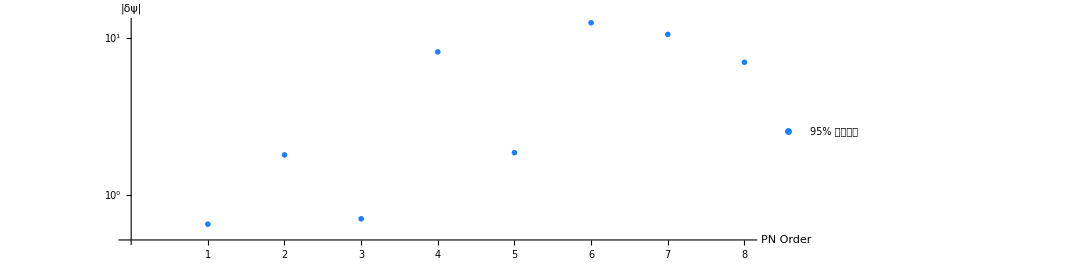

```mathematica
(*1. 你的核心计算：仅保留 95% 分位（上限），只算绝对值，不手动log！*)deviationOrders={0,2,3,4,"5l",6,"6l",7};
results=Table[key="cpsi"<>ToString[order];
(*只取95%分位+绝对值，就是论文的|δψ|上限*)Abs[Quantile[samples[key][key]/samples[key]["psi"<>ToString[order]],0.95]],{order,deviationOrders}];

(*2. 绘图：完全复刻论文样式*)
ListPlot[results,(*论文样式：蓝色星标*)PlotMarkers->{{"*",30}},PlotStyle->RGBColor[0.1,0.5,1],PlotLegends->{"95% 置信上限"},(*坐标轴：完全匹配论文*)AxesLabel->{"PN Order","|δψ|"},Ticks->{Range[Length[deviationOrders]],Automatic},(*✅ 关键：纵轴对数刻度（论文标准）*)ScalingFunctions->{"Linear","Log10"},(*网格+样式*)GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],BaseStyle->{FontSize->14,FontFamily->"Arial"},ImageSize->800]
```

### 0/2PN

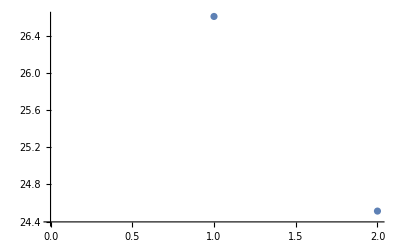

```mathematica
ListPlot[contourPoints[[n]][[2]][[1]]]
```

```mathematica
contourPoints[[n]][[2]][[1]]
contourPoints[[n]][[1]][[-1]]
```

{26.61,24.5131}

{24.5131,26.61}

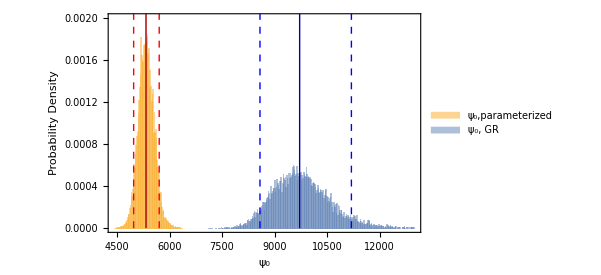

输入Mc范围：{23,42}

输入q范围：{1,4}

m1范围：{26.4201,100.894}

m2范围：{13.8129,48.2453}

对称数据：原始 56295 + 镜像 56295

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{13.8129, 100.894} × {13.8129, 100.894}

等高线值：{1.×10^-7}，共 2 条

第一条前3点：{{38.7766,39.0487},{38.7659,39.085},{38.7555,39.1208}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.999531

可信水平百分比：99.9531%

==========================

```mathematica
order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{23,42},{1,4}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0000000001};
contourPD[n]={0.0000001};
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n],"",True][[1]][[2]];
```

0.9999

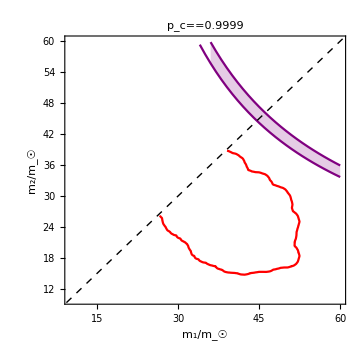

```mathematica
prob=0.9999
m1s=Range[10,60,1];
m2s=Range[10,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob/2];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[2]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

### 2/2PN

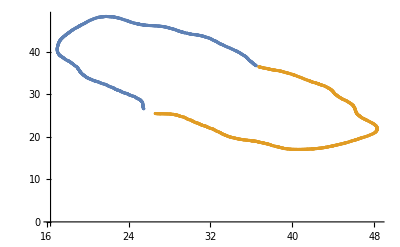

```mathematica
ListPlot[contourPoints[[n]]]
```

```mathematica
m1m2PDF[n][36,30]
```

0.0132577

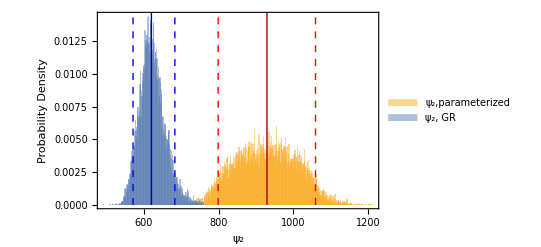

输入Mc范围：{23,42}

输入q范围：{1,4}

m1范围：{26.4201,100.894}

m2范围：{13.8129,48.2453}

对称数据：原始 62012 + 镜像 62012

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999997（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{13.8129, 100.894} × {13.8129, 100.894}

等高线值：{0.00022}，共 2 条

第一条前3点：{{28.0481,27.776},{28.1098,27.6948},{28.1199,27.6815}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.985573

可信水平百分比：98.5573%

==========================

```mathematica
order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{23,42},{1,4}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n],42,1];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.00022};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n],"",True][[1]][[2]];
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];*)
```

```mathematica
prob
```

0.985573

0.9856

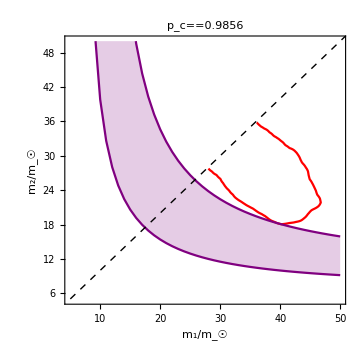

```mathematica
prob=0.9856
m1s=Range[5,50,1];
m2s=Range[5,50,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

### 3/2PN

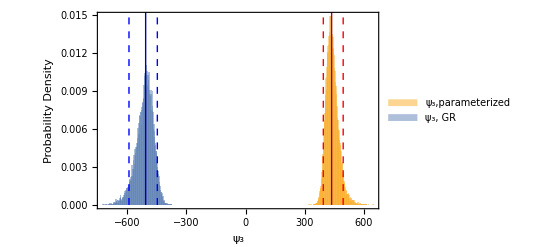

输入Mc范围：{23,42}

输入q范围：{1,4}

m1范围：{26.4201,100.894}

m2范围：{13.8129,48.2453}

原始数据量 = 83766，降采样后数据量 = 83766（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999998

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 7.61486×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：1 条

第一条等高线的前5个边界点：{{26.6654,28.2453},{26.6908,28.4445},{26.7513,28.5697},{26.9872,28.8319},{26.9944,28.919}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$524913条等高线 =====

包含闭合区域数：1

区域内总积分值：0.999988

可信水平百分比：99.9988%

==========================

```mathematica
order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{23,42},{1,4}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

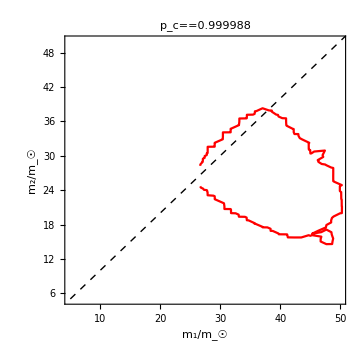

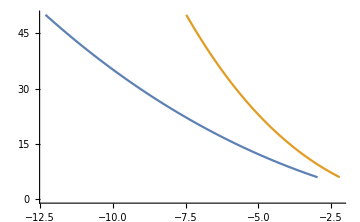

```mathematica
m1s=Range[5,50,1];
m2s=Range[5,50,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 4/2PN

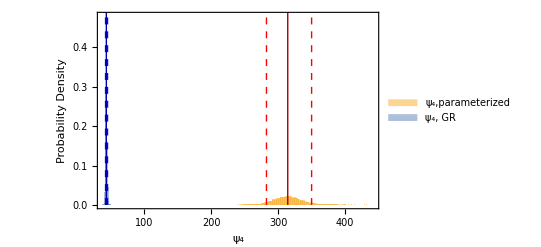

输入Mc范围：{23,42}

输入q范围：{1,4}

m1范围：{26.4201,100.894}

m2范围：{13.8129,48.2453}

原始数据量 = 60080，降采样后数据量 = 60080（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999975

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 5.73882×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.00001}

等高线数量：2 条

第一条等高线的前5个边界点：{{44.0422,14.0601},{44.2779,14.1646},{44.7583,14.4278},{45.0387,14.8138},{45.532,14.8146}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$529065条等高线 =====

包含闭合区域数：2

区域内总积分值：0.999828

可信水平百分比：99.9828%

==========================

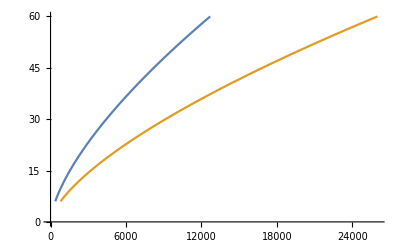

```mathematica
order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{23,42},{1,4}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.00001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

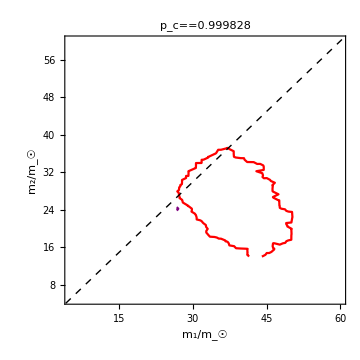

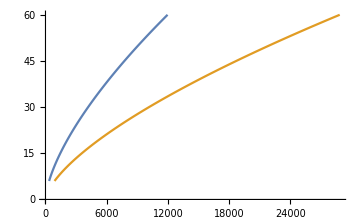

```mathematica
m1s=Range[5,60,1];
m2s=Range[5,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 5/2PN, log

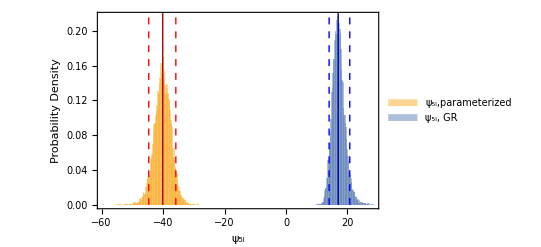

输入Mc范围：{23,42}

输入q范围：{1,4}

m1范围：{26.4201,100.894}

m2范围：{13.8129,48.2453}

原始数据量 = 59512，降采样后数据量 = 59512（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 5.32223×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：1 条

第一条等高线的前5个边界点：{{44.9172,15.0988},{45.0387,15.0571},{45.0928,15.0677},{47.6179,15.0799},{47.6985,15.4633}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$533491条等高线 =====

包含闭合区域数：1

区域内总积分值：0.999999

可信水平百分比：99.9999%

==========================

```mathematica
order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{23,42},{1,4}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

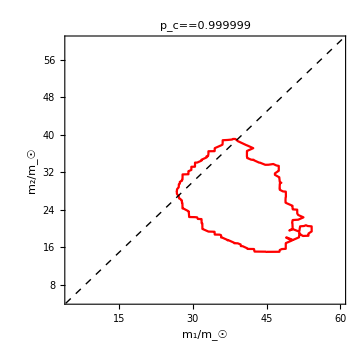

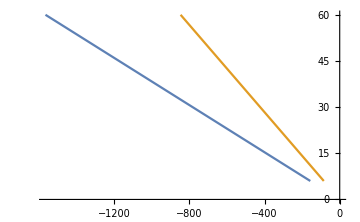

```mathematica
m1s=Range[5,60,1];
m2s=Range[5,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 6/2PN

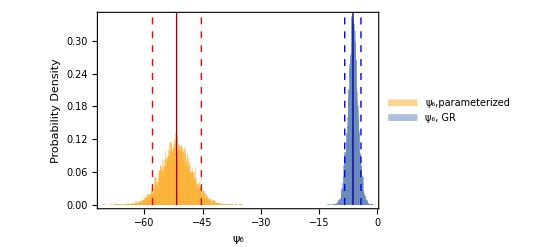

输入Mc范围：{23,42}

输入q范围：{1,4}

m1范围：{26.4201,100.894}

m2范围：{13.8129,48.2453}

原始数据量 = 63510，降采样后数据量 = 63510（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 8.14733×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：1 条

第一条等高线的前5个边界点：{{38.831,15.8618},{39.7191,15.5573},{39.8104,15.0849},{42.3198,15.07},{42.3789,15.0714}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$538117条等高线 =====

包含闭合区域数：1

区域内总积分值：0.999993

可信水平百分比：99.9993%

==========================

```mathematica
order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[{23,42},{1,4}];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

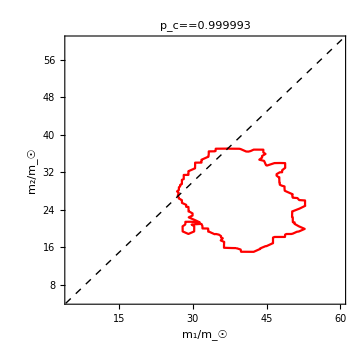

-Graphics-

```mathematica
m1s=Range[5,60,1];
m2s=Range[5,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 6/2PN, log

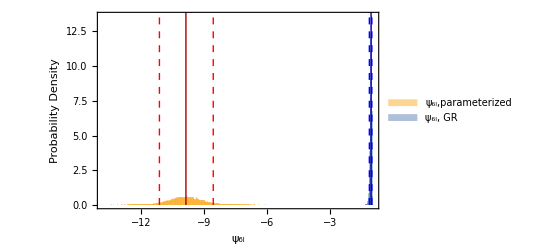

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 60053，降采样后数据量 = 60053（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 7.65235×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{1.×10^-6}

等高线数量：1 条

第一条等高线的前5个边界点：{{53.1703,19.7303},{53.1703,16.0881},{46.6907,16.0787},{46.3105,15.9304},{46.2857,14.0655}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$540533条等高线 =====

包含闭合区域数：1

区域内总积分值：0.99999

可信水平百分比：99.999%

==========================

```mathematica
order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.000001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];
```

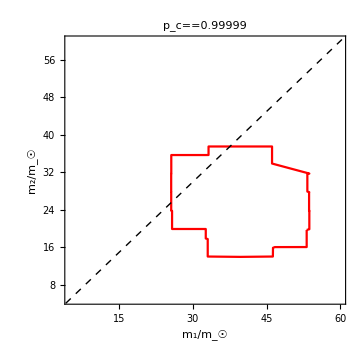

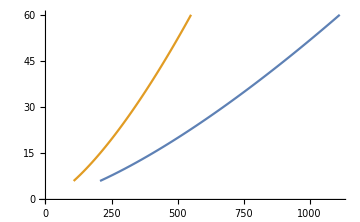

```mathematica
m1s=Range[5,60,1];
m2s=Range[5,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

### 7/2PN

```mathematica
contourPoints[n][[1]][[1]]
```

{28.656,25.1467}

```mathematica
m1m2PDF[n][contourPoints[n][[1]][[1]][[2]],contourPoints[n][[1]][[1]][[1]]]
```

0

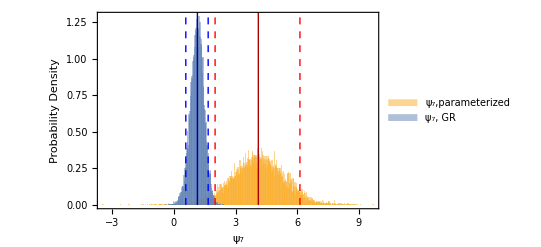

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

对称数据：原始 57196 + 镜像 57196

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 5.4155×10^-6 for the integral and error estimates.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 5.4155×10^-6 for the integral and error estimates.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{4.05769, 405.769} × {4.05769, 405.769}

等高线值：{0.000515}，共 2 条

第一条前3点：{{27.5471,28.8024},{27.343,28.9724},{27.1425,29.1645}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

[合并模式] 将 2 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: True)

区域内总积分值：0.964219

可信水平百分比：96.4219%

==========================

```mathematica
order=7;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
(*contourPD[n]={0.00115};*)
contourPD[n]={0.000515};
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n],"",True][[1]][[2]];
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];*)
```

```mathematica
prob
```

0.964219

0.9642

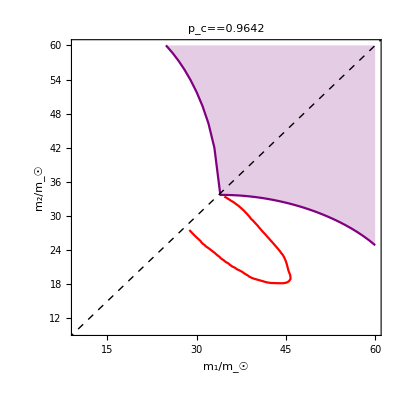

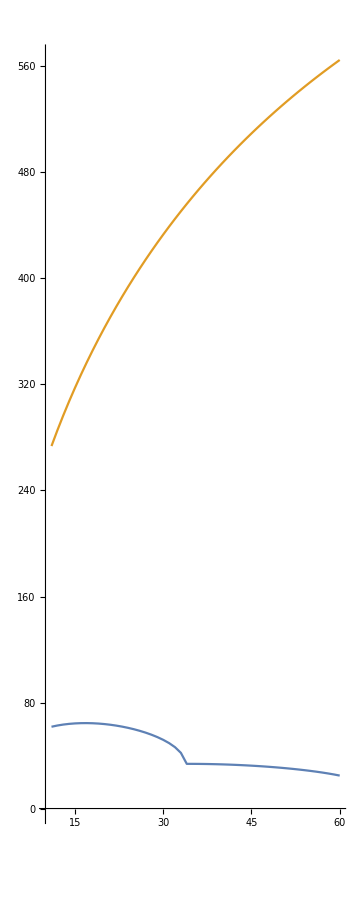

```mathematica
prob=0.9642
m1s=Range[10,60,1];
m2s=Range[10,60,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[2]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]},AspectRatio->Automatic]
```

```mathematica
combinedPlot=GraphicsGrid[
plots[{1,2,8}],
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

GraphicsGrid::list: Missing[KeyAbsent,{1,2,8}] is not a list of lists.

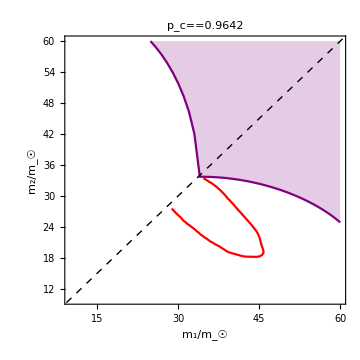
<|cpsi0→-Graphics-,cpsi2→-Graphics-,cpsi7→-Graphics-|>

```mathematica
plots
```

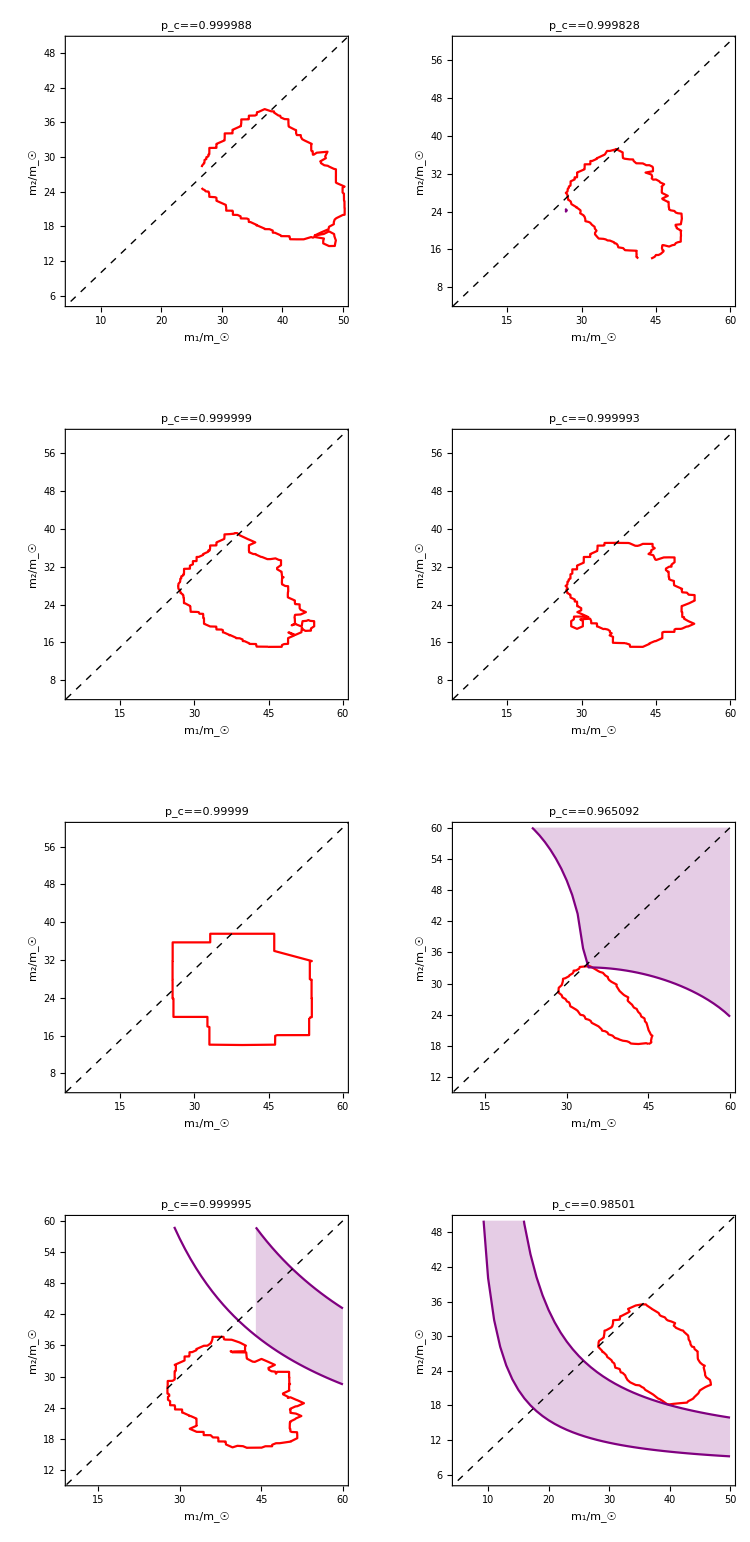

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

## (old) m1-m2 Plot, 22

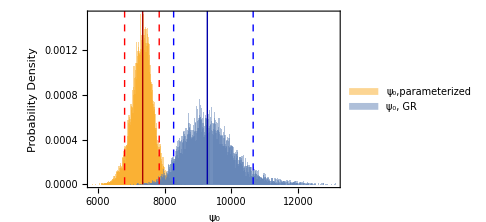

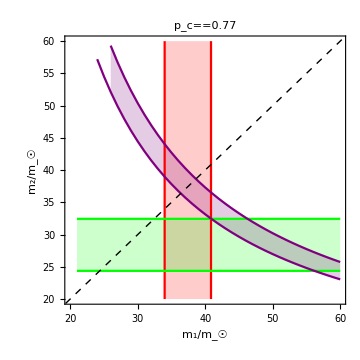

```mathematica
m1s=Range[20,60,1];
m2s=Range[20,60,1];

order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.77;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

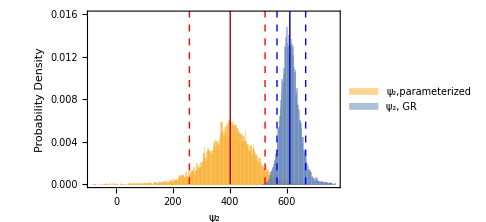

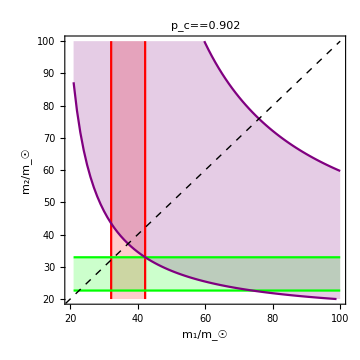

```mathematica
m1s=Range[20,100,1];
m2s=Range[20,100,1];

order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.902;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.902^3
```

0.266129

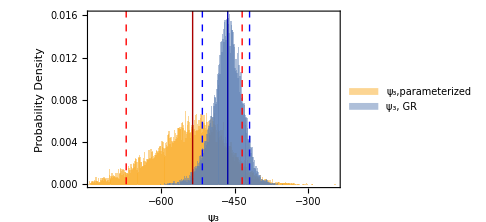

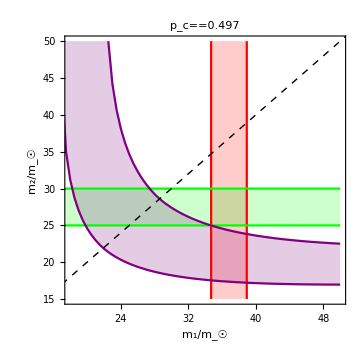

```mathematica
m1s=Range[15,50,1/2];
m2s=Range[15,50,1/2];

order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.497;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.495^3
```

0.878713

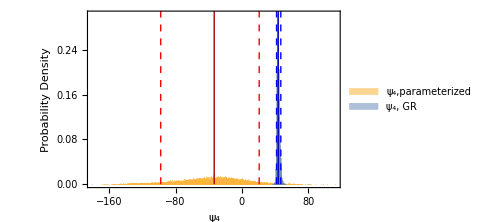

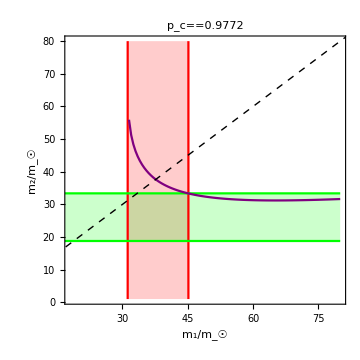

```mathematica
m1s=Range[1,80,1/2];
m2s=Range[1,80,1/2];

order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9772;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

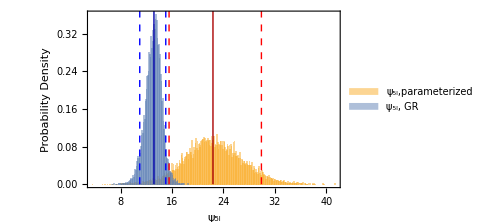

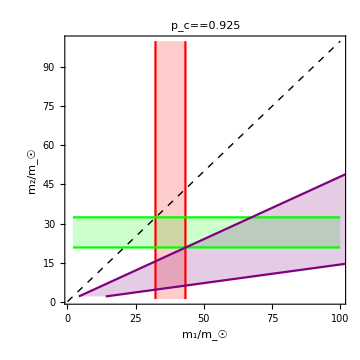

```mathematica
m1s=Range[1,100,1];
m2s=Range[1,100,1];

order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9250;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
BCI[n][n]
```

{15.535,22.3649,29.9001}

```mathematica
1-0.925^3
```

0.208547

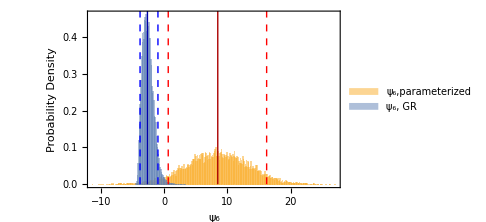

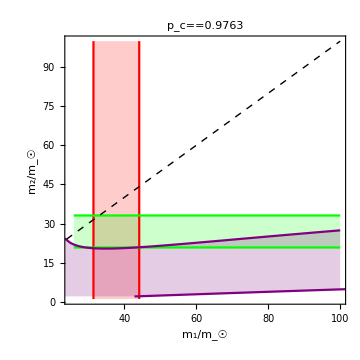

```mathematica
m1s=Range[25,100,1];
m2s=Range[1,100,1];

order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.9763;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

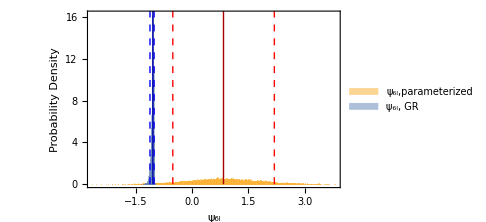

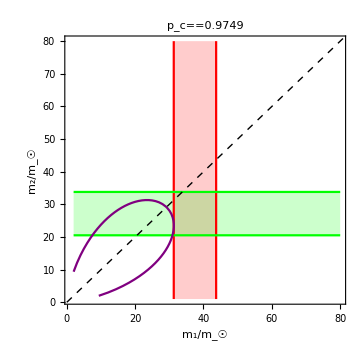

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9749;
(*prob=0.9891;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

Part::partw: Part 7 of … does not exist.

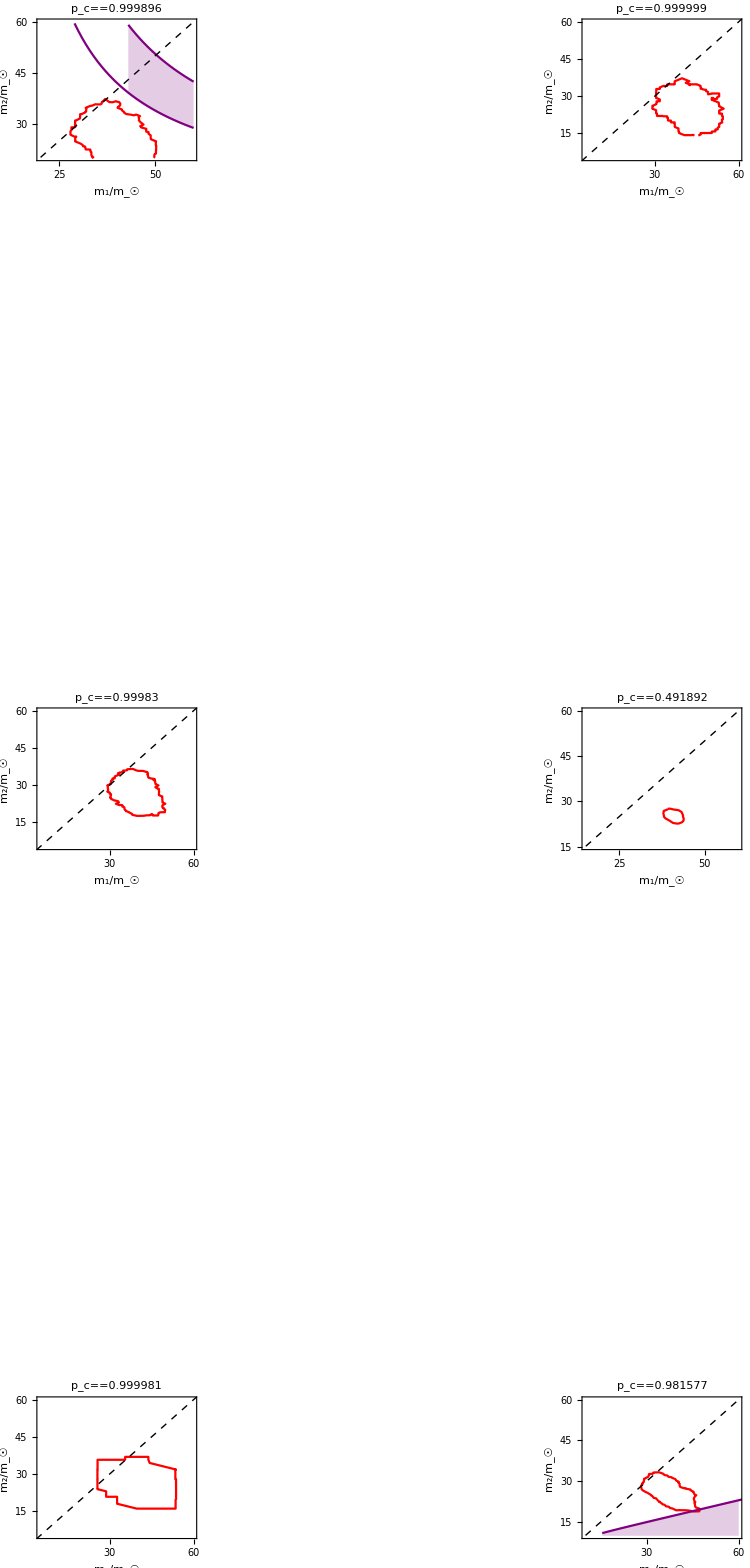

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

## Value Domains

```mathematica
vd=<||>;
```

```mathematica
(BCI["cpsi0"]["cpsi0"][[3]]-BCI["cpsi0"]["cpsi0"][[1]])/5000
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[0,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi0"]["mass1"][[1]],BCI["cpsi0"]["mass1"][[3]]},
{m2,BCI["cpsi0"]["mass2"][[1]],BCI["cpsi0"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False,
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]],TraditionalForm[Subscript[ψ,order]]}
],
{spin1z,BCI["cpsi0"]["spin1z"][[2]]},{spin2z,BCI["cpsi0"]["spin2z"][[2]]}
]
```

0.206569

```mathematica
(BCI["cpsi2"]["cpsi2"][[3]]-BCI["cpsi2"]["cpsi2"][[1]])/250
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[2,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi2"]["mass1"][[1]],BCI["cpsi2"]["mass1"][[3]]},
{m2,BCI["cpsi2"]["mass2"][[1]],BCI["cpsi2"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi2"]["spin1z"][[2]]},{spin2z,BCI["cpsi2"]["spin2z"][[2]]}
]
```

1.06474

```mathematica
(BCI["cpsi3"]["cpsi3"][[3]]-BCI["cpsi3"]["cpsi3"][[1]])/150
Manipulate[
Plot3D[
Function[{m1,m2},Psi[3,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi3"]["mass1"][[1]],BCI["cpsi3"]["mass1"][[3]]},
{m2,BCI["cpsi3"]["mass2"][[1]],BCI["cpsi3"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi3"]["spin1z"][[2]]},{spin2z,BCI["cpsi3"]["spin2z"][[2]]}
]
```

1.57419

Part::partw: Part 3 of Missing[KeyAbsent,cpsi3][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi3][mass1]⟦3⟧} is not a machine-sized real number.

```mathematica
(BCI["cpsi4"]["cpsi4"][[3]]-BCI["cpsi4"]["cpsi4"][[1]])/5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[4,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi4"]["mass1"][[1]],BCI["cpsi4"]["mass1"][[3]]},
{m2,BCI["cpsi4"]["mass2"][[1]],BCI["cpsi4"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi4"]["spin1z"][[2]]},{spin2z,BCI["cpsi4"]["spin2z"][[2]]}
]
```

23.7613

```mathematica
(BCI["cpsi5l"]["cpsi5l"][[3]]-BCI["cpsi5l"]["cpsi5l"][[1]])/1.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi5l"]["mass1"][[1]],BCI["cpsi5l"]["mass1"][[3]]},
{m2,BCI["cpsi5l"]["mass2"][[1]],BCI["cpsi5l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

9.56092

```mathematica
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,3,100},
{m2,3,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

```mathematica
(BCI["cpsi6"]["cpsi6"][[3]]-BCI["cpsi6"]["cpsi6"][[1]])/0.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[6,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6"]["mass1"][[1]],BCI["cpsi6"]["mass1"][[3]]},
{m2,BCI["cpsi6"]["mass2"][[1]],BCI["cpsi6"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6"]["spin1z"][[2]]},{spin2z,BCI["cpsi6"]["spin2z"][[2]]}
]
```

31.1398

```mathematica
(BCI["cpsi6l"]["cpsi6l"][[3]]-BCI["cpsi6l"]["cpsi6l"][[1]])/0.1
Manipulate[
Plot3D[
Function[{m1,m2},Psi["6l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6l"]["mass1"][[1]],BCI["cpsi6l"]["mass1"][[3]]},
{m2,BCI["cpsi6l"]["mass2"][[1]],BCI["cpsi6l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6l"]["spin1z"][[2]]},{spin2z,BCI["cpsi6l"]["spin2z"][[2]]}
]
```

27.0383

```mathematica
(*Manipulate[
Plot3D[
Function[{m1,m2},Psi[7,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,20,80},
{m2,20,80},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,0.06070798549182338},{spin2z,0.09392835788044217}
(*{spin1z,-1,1},{spin2z,-1,1}*)
]*)
```

## Exports

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/comp_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,compPlots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Export["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf",patch6,"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/value_domains/","GW150914_vd_",
name,
".pdf"];
Export[exportPath,vd[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

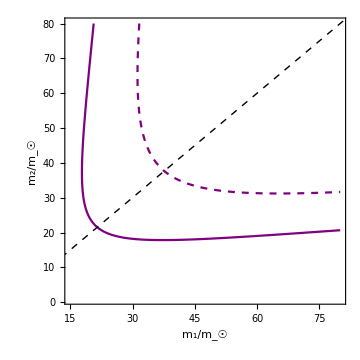

```mathematica
m1s=Range[15,80,1];
m2s=Range[1,80,1];

order=4;
n="cpsi"<>ToString[order];

prob1=0.9772;
(*再大一点会扫过这个矩形*)
prob2=0.989;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[Reverse[Reverse/@Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]]
(*tapes[n][n][[2]][[2;;]],
tapes[n][n][[4]][[2;;]]*)
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
]
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

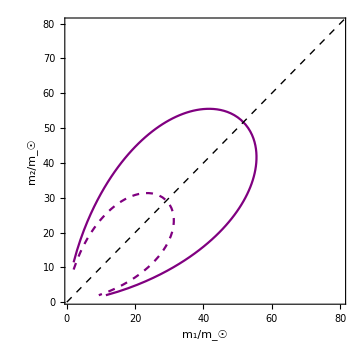

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];

prob1=0.9749;
prob2=0.9891;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Join[Reverse/@Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

patch6=ListLinePlot[
{
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
tapes[n][n][[1]][[2;;]],
tapes[n][n][[3]][[2;;]]
},
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
AspectRatio->1,
PlotRange->{{40.02,40.026},{30.015,30.020}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}]
},
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
],
Black,Dashed,Line[{{0,0},{100,100}}](*,
Inset[
patch6]*)
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

```mathematica
name="cpsi6l";
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
"_double",
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_inverse_plot_cpsi6l_double.pdf